# Exponential NDF

This is code to accompany the book:
A Hitchhiker’s Guide to Multiple Scattering
© 2020 Eugene d’Eon 
www.eugenedeon.com/hitchhikers

### notation

u = m . n = Cos[θ_m]
α  = roughness

## Definitions and derivations

```mathematica
Exponential`D[u_,α_]:=(2 ⅇ^(-(2 √(1-u^2))/(u α)))/(π u^4 α^2)HeavisideTheta[u]
```

### comparison to Beckmann and GGX

```mathematica
Clear[im];im[exp]:=-Graphics-;im[ggx]:=-Graphics-;im[beckmann]:=-Graphics-;
```

```mathematica
Manipulate[Show[im[s],ImageSize->512],{s,{exp,ggx,beckmann}}]
```

### relationship to Beckmann

The Exponential NDF can be written as a Gamma superposition of Beckmanns:

```mathematica
Integrate[Beckmann`D[u,α √m]PDF[GammaDistribution[3/2,1]][m],{m,0,Infinity},Assumptions->0<u<1&&α>0&&a>0]
```

(2 ⅇ^(-(2 √(1-u^2))/(u α)))/(π u^4 α^2)

or as a Chi-3 superposition:

```mathematica
Integrate[Beckmann`D[u,α/(√2) m]PDF[ChiDistribution[3]][m],{m,0,Infinity},Assumptions->0<u<1&&α>0&&a>0]
```

(2 ⅇ^(-(2 √(1-u^2))/(u α)))/(π u^4 α^2)

### importance sampling (for Walter’s method)

Use the Chi-3 expansion of the NDF we can sample the full NDF using 3 Gaussian random variates and 1 uniform random variate:

```mathematica
1/(√(1-(α/(√2) Norm[{Subscript[g, 1],Subscript[g, 2],Subscript[g, 3]}])^2 (Log[Subscript[u, 1]])))
```

1/(√(1-1/2 α^2 (Abs[g_1]^2+Abs[g_2]^2+Abs[g_3]^2) Log[u_1]))

General::munfl: Exp[-42566.1] is too small to represent as a normalized machine number; precision may be lost.

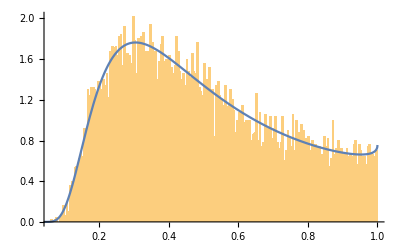

```mathematica
With[{α=2.3},
Show[
Histogram[Table[1/(√(1-(α/(√2) Norm[{RandomVariate[NormalDistribution[]],RandomVariate[NormalDistribution[]],RandomVariate[NormalDistribution[]]}])^2 (Log[RandomReal[]]))),{i,Range[10000]}],200,"PDF"],
Plot[Exponential`D[u,α]2 Pi u,{u,0,1},PlotRange->All]
]
]
```

### shape invariant f(x)

```mathematica
FullSimplify[Exponential`D[u,α] u^4 α^2/.u->1/(√(1+x^2 α^2)),Assumptions->1-1/(√(1+x^2 α^2))>0&&x>0&&α>0&&a>0]
```

(2 ⅇ^(-2 x))/π

### distribution of slopes

```mathematica
FullSimplify[Exponential`D[1/(√(p^2+q^2+1)),α](1/(√(p^2+q^2+1)))^4,Assumptions->0<α<1&&p>0&&q>0]
```

(2 ⅇ^(-(2 √(p^2+q^2))/α))/(π α^2)

```mathematica
Exponential`P22[p_,q_,α_]:=(2 ⅇ^(-(2 √(p^2+q^2))/α))/(π α^2)
```

```mathematica
Integrate[Exponential`P22[p,q,α],{p,-Infinity,Infinity},{q,-Infinity,Infinity},Assumptions->0<α<1]
```

1

### sigma - approximate with Ei sigma:

The cross section and Lambda() function are not known analytically, but we noted the following close approximation:

```mathematica
Ei`σ[u_,α_]:=1/(6 √π (-1+u^2) α^2)(α (3 √π u (-1+u^2) α+2 ⅇ^(u^2/((-1+u^2) α^2)) √(1-u^2) (-α^2+u^2 (-1+α^2)))+3 √π u (-α^2+u^2 (-2+α^2)) Erf[u/(√(1-u^2) α)]+2 √π u^2 Abs[u] (1+2 Erf[(u^2 √(1-u^2))/(α Abs[u]-u^2 α Abs[u])]))
```

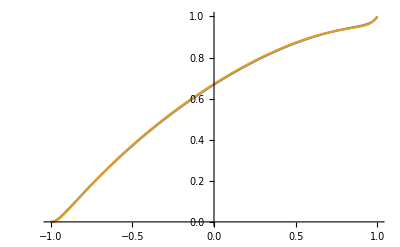

```mathematica
With[{α=2.1},
Plot[{
Quiet[NIntegrate[Exponential`D[ui,α]Delta`σ[u,ui],{ui,0,1}]],
Quiet[Ei`σ[u,1.7α]]
},{u,-1,1}]
]
```

### G1 shadow

```mathematica
Ei`Λ[u_,α_]:=(2 ⅇ^(u^2/((-1+u^2) α^2)) √(1-u^2) α (-α^2+u^2 (-1+α^2))+√π u (3 α^2+u^2 (2-3 α^2)) Erfc[u/(√(1-u^2) α)])/(6 √π u (-1+u^2) α^2)
```

```mathematica
Ei`G1[u_,α_]:=1/(1+Ei`Λ[u,α])
```

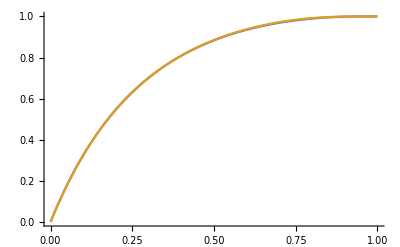

```mathematica
With[{α=.8},
Plot[{
Quiet[u/NIntegrate[Exponential`D[ui,α]Delta`σ[u,ui],{ui,0,1}]],
Quiet[Ei`G1[u,1.7α]]
},{u,0,1},PlotRange->All]
]
```

### Rational approximation for G1:

Similar to Walter’s approximation for Beckmann G1 we find:

```mathematica
Exponential`G1approx[u_,α_]:=If[#1<1.5,
(4.15428848706139*^-8+5.3171271839868055 #1+1.5604787398328208 #1^2)/(1+2.9490717540313374 #1+3.812617848664264 #1^2-1.0148658798039354 #1^3+0.18113230976734568 #1^4)
,
1]&[1/1.7 α^-1((√(1-u^2))/u)^-1]
```

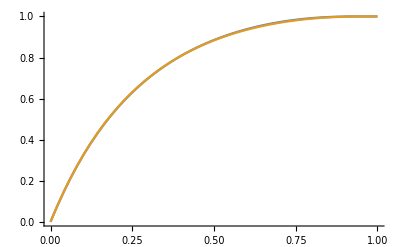

```mathematica
With[{α=0.8},
Plot[{
Exponential`G1approx[u,α],
u/Quiet[NIntegrate[Exponential`D[ui,α]Delta`σ[u,ui],{ui,0,1}]]
},{u,0,1},PlotRange->All]
]
```